Hello and Welcome! When working on projects, one of the tasks you may run into is reading and writing data. This data can be text files, or webpages, or video files, or sound files. Whatever the case may be, Mathematica has made it very easy for us to do this with its unified functions Import and Export.

### Directory Functions

As we get started with Import and Export, we’re going to need ways to refer to the folders in our computer. In order to make your notebooks work on Windows and Mac seamlessly, you should try to use these functions wherever possible.

The first function is Directory:

```mathematica
?Directory
```

RowBox[{"Directory", "[", "]"}] gives the current working directory.

Directory gives us the current working directory, which is where Import and Export will try to read and writes files:

```mathematica
Directory[]
```

/Users/shad

So my current working directory is /Users/shad.

We can use SetDirectory to change the current directory:

```mathematica
?SetDirectory
```

RowBox[{"SetDirectory", "[", StyleBox["\"\!\(\*StyleBox[\"dir\",\"TI\"]\)\"", ShowStringCharacters->True], "]"}] sets the current working directory to StyleBox["dir", "TI"]. 
RowBox[{"SetDirectory", "[", "]"}] sets the current working directory to your "home" directory.

So, for example, we can set the directory to the folder called Udemy:

```mathematica
SetDirectory["Udemy"]
```

/Users/shad/Udemy

So, Mathematica does not read and write files from the same directory as where your notebook file is located. You can ask Mathematica to tell you where your notebook file is located with NotebookDirectory:

```mathematica
?NotebookDirectory
```

RowBox[{"NotebookDirectory", "[", "]"}] gives the directory of the current evaluation notebook. 
RowBox[{"NotebookDirectory", "[", StyleBox["nb", "TI"], "]"}] gives the directory for the notebook specified by StyleBox["nb", "TI"].

So, my current notebook is located in:

```mathematica
NotebookDirectory[]
```

/Users/shad/Google Drive/Udemy/S02E25 - Import and Export/

We can set our current directory to the NotebookDirectory by passing it to SetDirectory:

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/shad/Google Drive/Udemy/S02E25 - Import and Export

Every time we change our directory, the previous directory is pushed onto a stack which we can get by using DirectoryStack:

```mathematica
?DirectoryStack
```

RowBox[{"DirectoryStack", "[", "]"}] gives the directory stack that represents the sequence of current directories used.

```mathematica
DirectoryStack[]
```

{/Users/shad/Udemy,/Users/shad}

And, we can pop previous directories off the stack and make them the current directory with ResetDirectory:

```mathematica
ResetDirectory[]
```

/Users/shad/Udemy

This functionality is especially useful if you write a function that needs to change the current directory to do something. At the end, the function should change the directory back to what it was before the function was called. You can SetDirectory at the beginning of the function, and then ResetDirectory at the end.

### Import

Great. Let’s take a look at how to import data into Mathematica.

#### Importing CSV files

```mathematica
?Import
```

RowBox[{"Import", "[", StyleBox["\"\!\(\*StyleBox[\"file\",\"TI\"]\)\"", ShowStringCharacters->True], "]"}] imports data from a file, returning a complete StyleBox["Wolfram Language", "RebrandingTerm"] version of it.
RowBox[{"Import", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"file\",\"TI\"]\)\"", ShowStringCharacters->True], ",", StyleBox["elements", "TI"]}], "]"}] imports the specified elements from a file.
RowBox[{"Import", "[", RowBox[{StyleBox["\"http://\!\(\*StyleBox[\"url\",\"TI\"]\)\"",ShowStringCharacters->True], ",", StyleBox["…", "TR"]}], "]"}] and RowBox[{"Import", "[", RowBox[{StyleBox["\"ftp://\!\(\*StyleBox[\"url\",\"TI\"]\)\"",ShowStringCharacters->True], ",", StyleBox["…", "TR"]}], "]"}] import from any accessible URL.

Let’s start simple. Suppose we had a Comma Seperated Value file, “CSVDemo.csv” in our Udemy directory. In order to import it we would say:

```mathematica
csvdata = Import["CSVDemo.csv"]
```

{{Albert,Einstein,Sciencing},{Fred,Astaire,Dancing},{Lionel,Messi,Footballing},{Bill,Gates,Computering}}

Let’s look at the data structure of what is returned.

```mathematica
Head[csvdata]
```

List

```mathematica
csvdata//Length
```

4

```mathematica
csvdata//TableForm
```

Albert | Einstein | Sciencing
Fred | Astaire | Dancing
Lionel | Messi | Footballing
Bill | Gates | Computering

Mathematica is pretty smart at figuring out what kind of file it is importing. In this case, it recognized that it is dealing with a csv file. It then partitioned the data at the commas, and return characters and formatted it into a useful data structure, namely list of lists in this case. If necessary, we can give the format of the file as a second argument.

```mathematica
data=Import["CSVDemo.csv","csv"]
```

{{Albert,Einstein,Sciencing},{Fred,Astaire,Dancing},{Lionel,Messi,Footballing},{Bill,Gates,Computering}}

You can use import to import all kinds of files such as excel files, pdfs, giffs, pngs, jpgs, and so on. Please have a look in the documentation center for the different file formats Import supports.

#### Importing a file from a URL:

Often times we will need a file from the web. Import can load files from URLs. For example let’s say we were interested in importing the list of all the words in the English language.

```mathematica
words=StringSplit[Import["http://www-01.sil.org/linguistics/wordlists/english/wordlist/wordsEn.txt"],"\n"]
```

{a,aah,aahed,aahing,aahs,aardvark,aardvarks,aardwolf,ab,109565,zymase,zymogenic,zymology,zymolysis,zymoplastic,zymoscope,zymurgy,zyzzyva,zyzzyvas}
 |  |  |  |

#### Importing a webpage.

In general, you can import any generic webpage. By default Mathematica will scrape alll the text on the page and return it as one giant string.

```mathematica
cnn=Import["http://www.cnn.com"]
```

But this may not be all that useful depending on what you are doing. Every time Mathematica imports a file or a URL, it converts it to a Mathematica object which carries certain metadata, which we can ask for with “Elements”:

```mathematica
cnn=Import["http://www.cnn.com","Elements"]
```

{Data,FullData,Hyperlinks,ImageLinks,Images,Plaintext,Source,Title,XMLObject}

We can ask Mathematica to return any of these types of data. For example:

```mathematica
cnn=Import["http://www.cnn.com","Title"]
```

CNN - Breaking News, Latest News and Videos

Let’s look at a cuter example. Let’s head over to google images and search for owls. Let’s import this page and ask for the “Images”.

```mathematica
Import["https://www.google.com/search?q=owls&hl=en&biw=1399&bih=775&site=webhp&source=lnms&tbm=isch&sa=X&ved=0ahUKEwishLHI68nNAhUJzIMKHUSCC4IQ_AUIBigB","Images"]
```

“Images” here is one of the elements available for this import:

```mathematica
Import["https://www.google.com/search?q=owls&hl=en&biw=1399&bih=775&site=webhp&source=lnms&tbm=isch&sa=X&ved=0ahUKEwishLHI68nNAhUJzIMKHUSCC4IQ_AUIBigB","Elements"]
```

As you can see we can get plain text, the URL of each image and so on.

#### Gif

Let’s head over to giphy and import it into Mathematica:

```mathematica
gif=Import["http://i755.photobucket.com/albums/xx195/skez520mia/FUNNY%20CRAZY%20AND%20AWESOME%20GIFS/Stare-down-dog-slaps.gif","gif"]
```

```mathematica
Animate[u,{u,gif}]
```

#### Names

Now let’s look at a more practical example. Let’s download some census data on the popular baby names for girls and see how it changes over time. Here, we searched data.gov for baby girl names. Let’s copy the CSV link and import it as rawNameData. We have to drop the first row as it is simply a header.

```mathematica
rawNameData=Drop[Import["https://data.illinois.gov/api/views/rx64-7qfr/rows.csv","csv"],1]
```

{{1,1980,Jennifer,3017},{2,1980,Amanda,1750},{3,1980,Melissa,1566},{4,1980,Sarah,1390},{5,1980,Jessica,1373},{6,1980,Nicole,1336},{7,1980,Elizabeth,1221},{8,1980,Michelle,1170},{9,1980,Amy,1013},{10,1980,Tiffany,941},{11,1980,Angela,924},{12,1980,Kelly,895},{13,1980,Heather,893},{14,1980,Kimberly,854},{15,1980,Lisa,845},{16,1980,Stephanie,839},{17,1980,Christina,778},{18,1980,Rebecca,757},{19,1980,Laura,756},{20,1980,Erin,736},{21,1980,Mary,655},{22,1980,Jamie,630},{23,1980,Megan,604},{24,1980,Rachel,603},{25,1980,Sara,601},{1,1981,Jennifer,2920},{2,1981,Jessica,1683},{3,1981,Amanda,1607},{4,1981,Sarah,1565},{5,1981,Melissa,1401},{6,1981,Nicole,1341},{7,1981,Elizabeth,1221},{8,1981,Michelle,1024},{9,1981,Amy,1015},{10,1981,Stephanie,976},{11,1981,Tiffany,921},{12,1981,Rebecca,893},{13,1981,Kimberly,805},{14,1981,Angel,804},{15,1981,Lisa,778},{16,1981,Erin,771},{17,1981,Heather,770},{18,1981,Laura,742},{19,1981,Kelly,708},{20,1981,Christina,636},{21,1981,Sara,625},{22,1981,Mary,624},{23,1981,Kristin,599},{24,1981,Rachel,596},{25,1981,Jamie,590},{1,1982,Jennifer,2809},{2,1982,Jessica,1869},{3,1982,Amanda,1547},{4,1982,Nicole,1517},{5,1982,Sarah,1443},{6,1982,Elizabeth,1241},{7,1982,Melissa,1219},{8,1982,Stephanie,1046},{9,1982,Michelle,1023},{10,1982,Amy,987},{11,1982,Tiffany,902},{12,1982,Erin,803},{13,1982,Rebecca,778},{14,1982,Laura,772},{15,1982,Kimberly,746},{16,1982,Rachel,738},{17,1982,Lisa,721},{18,1982,Kelly,698},{19,1982,Angela,697},{20,1982,Heather,692},{21,1982,Crystal,655},{22,1982,Lauren,605},{23,1982,Christina,600},{24,1982,Megan,597},{25,1982,Amber,588},{1,1983,Jennifer,2636},{2,1983,Jessica,1847},{3,1983,Amanda,1493},{4,1983,Nicole,1429},{5,1983,Sarah,1358},{6,1983,Ashley,1338},{7,1983,Elizabeth,1175},{8,1983,Melissa,1146},{9,1983,Stephanie,1073},{10,1983,Michelle,918},{11,1983,Amy,894},{12,1983,Megan,845},{13,1983,Heather,835},{14,1983,Tiffany,822},{15,1983,Erin,812},{16,1983,Rebecca,730},{17,1983,Rachel,729},{18,1983,Laura,726},{19,1983,Kimberly,714},{20,1983,Lauren,704},{21,1983,Christina,678},{22,1983,Kelly,655},{23,1983,Crystal,651},{24,1983,Lisa,631},{25,1983,Katherine,629},{1,1984,Jennifer,2528},{2,1984,Jessica,1844},{3,1984,Ashley,1577},{4,1984,Amanda,1513},{5,1984,Nicole,1328},{6,1984,Sarah,1305},{7,1984,Elizabeth,1182},{8,1984,Melissa,1111},{9,1984,Stephanie,1087},{10,1984,Megan,933},{11,1984,Michelle,861},{12,1984,Heather,851},{13,1984,Amy,841},{14,1984,Rachel,824},{15,1984,Tiffany,801},{16,1984,Lauren,766},{17,1984,Laura,753},{18,1984,Danielle,711},{19,1984,Kelly,707},{20,1984,Erin,703},{21,1984,Christina,681},{22,1984,Kimberly,666},{23,1984,Rebecca,642},{24,1984,Emily,623},{25,1984,Katherine,608},{1,1985,Jennifer,2096},{2,1985,Ashley,2030},{3,1985,Jessica,1951},{4,1985,Amanda,1711},{5,1985,Nicole,1244},{6,1985,Sarah,1200},{7,1985,Elizabeth,1146},{8,1985,Megan,1120},{9,1985,Stephanie,1088},{10,1985,Melissa,1035},{11,1985,Lauren,857},{12,1985,Heather,838},{13,1985,Laura,836},{14,1985,Rachel,830},{15,1985,Christina,817},{16,1985,Michelle,796},{17,1985,Amy,769},{18,1985,Brittany,714},{19,1985,Danielle,702},{20,1985,Emily,667},{21,1985,Kimberly,656},{22,1985,Rebecca,641},{23,1985,Kelly,640},{24,1985,Erin,628},{25,1985,Katherine,611},{1,1986,Jessica,2198},{2,1986,Ashley,2103},{3,1986,Jennifer,1793},{4,1986,Amanda,1321},{5,1986,Sarah,1161},{6,1986,Stephanie,1132},{7,1986,Nicole,1080},{8,1986,Elizabeth,1001},{9,1986,Brittany,952},{10,1986,Lauren,942},{11,1986,Megan,864},{12,1986,Melissa,788},{13,1986,Laura,751},{14,1986,Samantha,736},{15,1986,Amy,730},{16,1986,Michelle,725},{17,1986,Heather,724},{18,1986,Rachel,693},{19,1986,Emily,665},{20,1986,Amber,664},{21,1986,Danielle,646},{22,1986,Christina,628},{23,1986,Katherine,608},{24,1986,Kelly,608},{25,1986,Kimberly,602},{25,1986,Tiffany,602},{1,1987,Ashley,2565},{2,1987,Jessica,2521},{3,1987,Amanda,1742},{4,1987,Jennifer,1609},{5,1987,Sarah,1349},{6,1987,Nicole,1128},{7,1987,Stephanie,1105},{8,1987,Brittany,1056},{9,1987,Elizabeth,1040},{10,1987,Samantha,998},{11,1987,Lauren,908},{12,1987,Megan,883},{13,1987,Melissa,841},{14,1987,Emily,802},{15,1987,Danielle,784},{16,1987,Michelle,718},{17,1987,Heather,709},{18,1987,Rachel,701},{19,1987,Laura,678},{20,1987,Tiffany,634},{21,1987,Amy,630},{22,1987,Christina,612},{23,1987,Amber,585},{24,1987,Kelly,567},{25,1987,Katherine,552},{1,1988,Jessica,2275},{2,1988,Ashley,2264},{3,1988,Amanda,1686},{4,1988,Jennifer,1328},{5,1988,Sarah,1299},{6,1988,Brittany,1223},{7,1988,Samantha,1150},{8,1988,Stephanie,1115},{9,1988,Elizabeth,1092},{10,1988,Lauren,1063},{11,1988,Nicole,1045},{12,1988,Megan,881},{13,1988,Emily,824},{14,1988,Melissa,807},{15,1988,Danielle,784},{16,1988,Rachel,775},{17,1988,Michelle,718},{18,1988,Heather,716},{19,1988,Tiffany,669},{20,1988,Amber,645},{21,1988,Katherine,613},{22,1988,Christina,585},{23,1988,Laura,567},{24,1988,Rebecca,561},{25,1988,Kelly,555},{1,1989,Ashley,2308},{2,1989,Jessica,2031},{3,1989,Amanda,1610},{4,1989,Brittany,1562},{5,1989,Sarah,1338},{6,1989,Samantha,1276},{7,1989,Stephanie,1203},{8,1989,Jennifer,1156},{9,1989,Elizabeth,1070},{10,1989,Lauren,1063},{11,1989,Nicole,1040},{12,1989,Megan,999},{13,1989,Emily,865},{14,1989,Michelle,776},{15,1989,Danielle,731},{16,1989,Melissa,708},{17,1989,Rachel,694},{18,1989,Christina,659},{19,1989,Heather,652},{20,1989,Amber,640},{21,1989,Katherine,618},{22,1989,Rebecca,605},{23,1989,Jasmine,596},{24,1989,Tiffany,594},{25,1989,Kelly,587},{1,1990,Jessica,2117},{2,1990,Ashley,2098},{3,1990,Brittany,1533},{4,1990,Amanda,1504},{5,1990,Samantha,1312},{6,1990,Stephanie,1240},{7,1990,Sarah,1151},{8,1990,Elizabeth,1100},{9,1990,Jennifer,1081},{10,1990,Lauren,1064},{11,1990,Nicole,961},{12,1990,Emily,956},{13,1990,Megan,947},{14,1990,Michelle,785},{15,1990,Rachel,749},{16,1990,Melissa,720},{17,1990,Jasmine,696},{18,1990,Danielle,678},{19,1990,Rebecca,678},{20,1990,Katherine,621},{21,1990,Courtney,620},{22,1990,Kayla,598},{23,1990,Amber,574},{24,1990,Alyssa,566},{25,1990,Laura,553},{1,1991,Jessica,2075},{2,1991,Ashley,1906},{3,1991,Samantha,1313},{4,1991,Brittany,1286},{5,1991,Sarah,1220},{6,1991,Amanda,1178},{7,1991,Stephanie,1142},{8,1991,Elizabeth,1133},{9,1991,Emily,1083},{10,1991,Jennifer,1026},{11,1991,Megan,955},{12,1991,Lauren,895},{13,1991,Nicole,856},{14,1991,Rachel,806},{15,1991,Danielle,695},{16,1991,Melissa,693},{17,1991,Jasmine,689},{18,1991,Rebecca,669},{19,1991,Michelle,660},{20,1991,Kayla,642},{21,1991,Katherine,618},{22,1991,Kelsey,600},{23,1991,Alyssa,539},{24,1991,Amber,526},{25,1991,Courtney,511},{1,1992,Jessica,1816},{2,1992,Ashley,1744},{3,1992,Samantha,1189},{4,1992,Sarah,1095},{5,1992,Emily,1087},{6,1992,Brittany,1065},{7,1992,Amanda,1057},{8,1992,Elizabeth,1032},{9,1992,Stephanie,989},{10,1992,Jennifer,912},{11,1992,Megan,896},{12,1992,Lauren,861},{13,1992,Nicole,845},{14,1992,Rachel,798},{15,1992,Taylor,728},{16,1992,Danielle,709},{17,1992,Jasmine,652},{18,1992,Rebecca,632},{19,1992,Melissa,595},{20,1992,Michelle,579},{21,1992,Kayla,574},{22,1992,Kelsey,571},{23,1992,Alexandra,544},{24,1992,Katherine,540},{25,1992,Amber,521},{1,1993,Jessica,1789},{2,1993,Ashley,1573},{3,1993,Samantha,1195},{4,1993,Emily,1181},{5,1993,Sarah,1116},{6,1993,Taylor,1004},{7,1993,Brittany,953},{8,1993,Amanda,920},{9,1993,Elizabeth,915},{10,1993,Lauren,901},{11,1993,Nicole,881},{12,1993,Stephanie,880},{13,1993,Jennifer,800},{14,1993,Megan,788},{15,1993,Jasmine,757},{16,1993,Rachel,745},{17,1993,Danielle,614},{18,1993,Hannah,600},{19,1993,Rebecca,592},{20,1993,Michelle,588},{21,1993,Alyssa,587},{22,1993,Kayla,566},{23,1993,Kelsey,551},{24,1993,Melissa,546},{25,1993,Amber,542},{1,1994,Jessica,1640},{2,1994,Ashley,1300},{3,1994,Emily,1157},{4,1994,Samantha,1134},{5,1994,Taylor,1018},{6,1994,Sarah,1011},{7,1994,Nicole,902},{8,1994,Amanda,865},{9,1994,Brittany,825},{10,1994,Elizabeth,811},{11,1994,Megan,810},{12,1994,Stephanie,791},{13,1994,Lauren,779},{14,1994,Rachel,732},{15,1994,Jennifer,697},{16,1994,Jasmine,673},{17,1994,Danielle,662},{18,1994,Alexis,635},{19,1994,Hannah,627},{20,1994,Kayla,609},{21,1994,Rebecca,558},{22,1994,Michelle,551},{23,1994,Alyssa,539},{24,1994,Alexandra,501},{25,1994,Katherine,486},{1,1995,Jessica,1429},{2,1995,Ashley,1171},{3,1995,Emily,1169},{4,1995,Samantha,1103},{5,1995,Sarah,972},{6,1995,Taylor,936},{7,1995,Elizabeth,821},{8,1995,Rachel,806},{9,1995,Hannah,782},{10,1995,Megan,754},{11,1995,Amanda,730},{12,1995,Stephanie,721},{13,1995,Lauren,705},{14,1995,Alexis,684},{15,1995,Nicole,684},{16,1995,Brittany,670},{17,1995,Jennifer,645},{18,1995,Kayla,612},{19,1995,Jasmine,599},{20,1995,Brianna,538},{21,1995,Alyssa,534},{22,1995,Alexandra,521},{23,1995,Rebecca,518},{24,1995,Danielle,496},{25,1995,Morgan,489},{1,1996,Jessica,1265},{2,1996,Emily,1172},{3,1996,Ashley,1041},{4,1996,Samantha,962},{5,1996,Sarah,914},{6,1996,Taylor,902},{7,1996,Elizabeth,835},{8,1996,Alexis,816},{9,1996,Hannah,783},{10,1996,Rachel,740},{11,1996,Megan,720},{12,1996,Stephanie,646},{13,1996,Nicole,641},{14,1996,Jennifer,640},{15,1996,Lauren,632},{16,1996,Kayla,623},{17,1996,Amanda,607},{18,1996,Alyssa,584},{19,1996,Brittany,582},{20,1996,Rebecca,541},{21,1996,Brianna,527},{22,1996,Jasmine,523},{23,1996,Alexandra,498},{24,1996,Abigail,479},{25,1996,Morgan,460},{1,1997,Emily,1213},{2,1997,Jessica,1122},{3,1997,Samantha,1005},{4,1997,Hannah,945},{5,1997,Sarah,902},{6,1997,Ashley,884},{7,1997,Alexis,873},{8,1997,Taylor,832},{9,1997,Elizabeth,753},{10,1997,Megan,702},{11,1997,Rachel,670},{12,1997,Jennifer,630},{13,1997,Lauren,622},{14,1997,Alyssa,610},{15,1997,Nicole,594},{16,1997,Kayla,555},{17,1997,Abigail,548},{18,1997,Amanda,543},{19,1997,Stephanie,541},{20,1997,Brianna,534},{21,1997,Madison,508},{22,1997,Jasmine,484},{23,1997,Brittany,476},{24,1997,Olivia,476},{25,1997,Rebecca,449},{1,1998,Emily,1211},{2,1998,Samantha,1031},{3,1998,Jessica,978},{4,1998,Alexis,938},{5,1998,Hannah,878},{6,1998,Ashley,861},{7,1998,Sarah,827},{8,1998,Taylor,789},{9,1998,Elizabeth,700},{10,1998,Alyssa,661},{11,1998,Lauren,644},{12,1998,Megan,643},{13,1998,Abigail,597},{14,1998,Madison,596},{15,1998,Kayla,594},{16,1998,Jennifer,592},{17,1998,Rachel,557},{18,1998,Emma,542},{19,1998,Nicole,539},{20,1998,Brianna,497},{21,1998,Stephanie,496},{22,1998,Olivia,487},{23,1998,Amanda,477},{24,1998,Allison,466},{25,1998,Jasmine,465},{1,1999,Emily,1210},{2,1999,Hannah,958},{3,1999,Samantha,901},{4,1999,Jessica,898},{5,1999,Alexis,876},{6,1999,Elizabeth,809},{7,1999,Sarah,795},{8,1999,Taylor,706},{9,1999,Ashley,705},{10,1999,Grace,637},{11,1999,Lauren,633},{12,1999,Madison,630},{13,1999,Emma,629},{14,1999,Alyssa,606},{15,1999,Abigail,599},{16,1999,Jennifer,592},{17,1999,Kayla,586},{18,1999,Nicole,560},{19,1999,Megan,556},{20,1999,Brianna,522},{21,1999,Olivia,509},{22,1999,Rachel,493},{23,1999,Sydney,489},{24,1999,Natalie,461},{25,1999,Julia,435},{1,2000,Emily,1205},{2,2000,Hannah,1041},{3,2000,Jessica,843},{4,2000,Alexis,841},{5,2000,Samantha,816},{6,2000,Grace,762},{7,2000,Elizabeth,739},{8,2000,Ashley,733},{9,2000,Madison,715},{10,2000,Sarah,694},{11,2000,Kayla,656},{12,2000,Lauren,653},{13,2000,Alyssa,651},{14,2000,Olivia,646},{15,2000,Emma,624},{16,2000,Abigail,607},{17,2000,Taylor,600},{18,2000,Megan,573},{19,2000,Brianna,533},{20,2000,Jennifer,516},{21,2000,Anna,490},{22,2000,Rachel,477},{23,2000,Sydney,476},{24,2000,Natalie,471},{25,2000,Nicole,459},{1,2001,Emily,1182},{2,2001,Hannah,882},{3,2001,Jessica,793},{4,2001,Grace,778},{5,2001,Madison,763},{6,2001,Samantha,763},{7,2001,Abigail,738},{8,2001,Alexis,727},{9,2001,Elizabeth,710},{10,2001,Olivia,666},{11,2001,Ashley,658},{12,2001,Emma,656},{13,2001,Sarah,652},{14,2001,Alyssa,621},{15,2001,Kayla,593},{16,2001,Taylor,580},{17,2001,Lauren,561},{18,2001,Anna,516},{19,2001,Jennifer,511},{20,2001,Megan,504},{21,2001,Brianna,484},{22,2001,Nicole,462},{23,2001,Julia,460},{24,2001,Sydney,455},{25,2001,Rachel,432},{1,2002,Emily,1117},{2,2002,Emma,838},{3,2002,Madison,792},{4,2002,Olivia,790},{5,2002,Grace,775},{6,2002,Hannah,771},{7,2002,Abigail,735},{8,2002,Ashley,667},{9,2002,Samantha,661},{10,2002,Alexis,651},{11,2002,Elizabeth,636},{12,2002,Jessica,630},{13,2002,Alyssa,574},{14,2002,Sarah,570},{15,2002,Isabella,568},{16,2002,Lauren,537},{17,2002,Kayla,526},{18,2002,Taylor,491},{19,2002,Anna,479},{20,2002,Brianna,459},{21,2002,Natalie,443},{22,2002,Jennifer,428},{23,2002,Megan,428},{24,2002,Sophia,414},{25,2002,Sydney,400},{1,2003,Emily,1132},{2,2003,Emma,1046},{3,2003,Olivia,808},{4,2003,Abigail,793},{5,2003,Grace,777},{6,2003,Madison,736},{7,2003,Elizabeth,686},{8,2003,Alexis,680},{9,2003,Hannah,659},{10,2003,Ashley,644},{11,2003,Isabella,614},{12,2003,Samantha,592},{13,2003,Jessica,582},{14,2003,Sarah,582},{15,2003,Kayla,542},{16,2003,Alyssa,532},{17,2003,Lauren,479},{18,2003,Brianna,471},{19,2003,Anna,460},{20,2003,Natalie,456},{21,2003,Sophia,454},{22,2003,Taylor,407},{23,2003,Jennifer,406},{24,2003,Julia,396},{25,2003,Mia,393},{1,2004,Emily,1094},{2,2004,Emma,885},{3,2004,Olivia,797},{4,2004,Abigail,748},{5,2004,Madison,732},{6,2004,Grace,717},{7,2004,Isabella,679},{8,2004,Ashley,661},{9,2004,Elizabeth,641},{10,2004,Samantha,604},{11,2004,Hannah,592},{12,2004,Sarah,572},{13,2004,Alexis,557},{14,2004,Alyssa,523},{15,2004,Jessica,497},{16,2004,Sophia,480},{17,2004,Anna,477},{18,2004,Natalie,453},{19,2004,Lauren,450},{20,2004,Mia,432},{21,2004,Kayla,426},{22,2004,Ava,418},{23,2004,Brianna,403},{24,2004,Julia,399},{25,2004,Ella,387},{1,2005,Emily,1015},{2,2005,Emma,840},{3,2005,Olivia,797},{4,2005,Isabella,735},{5,2005,Abigail,721},{6,2005,Ava,643},{7,2005,Grace,642},{8,2005,Samantha,607},{9,2005,Elizabeth,596},{10,2005,Mia,591},{11,2005,Madison,589},{12,2005,Hannah,586},{13,2005,Sophia,566},{14,2005,Ashley,559},{15,2005,Natalie,520},{16,2005,Alexis,489},{17,2005,Ella,443},{18,2005,Alyssa,420},{19,2005,Jessica,420},{20,2005,Lauren,411},{21,2005,Sarah,404},{22,2005,Anna,395},{23,2005,Julia,390},{24,2005,Alexandra,372},{25,2005,Kayla,360},{1,2006,EMILY,937},{2,2006,EMMA,828},{3,2006,ISABELLA,828},{4,2006,OLIVIA,820},{5,2006,AVA,739},{6,2006,ABIGAIL,706},{7,2006,MADISON,671},{8,2006,GRACE,650},{9,2006,SOPHIA,636},{10,2006,MIA,616},{11,2006,SAMANTHA,602},{12,2006,HANNAH,577},{13,2006,ELIZABETH,561},{14,2006,ASHLEY,492},{15,2006,NATALIE,473},{16,2006,ELLA,465},{17,2006,ALEXIS,437},{18,2006,SARAH,433},{19,2006,CHLOE,397},{20,2006,ADDISON,391},{21,2006,BRIANNA,385},{22,2006,LAUREN,382},{23,2006,ALYSSA,377},{24,2006,JULIA,371},{25,2006,KAYLA,371},{1,2007,ISABELLA,893},{2,2007,OLIVIA,874},{3,2007,EMILY,815},{4,2007,SOPHIA,815},{5,2007,AVA,797},{6,2007,EMMA,794},{7,2007,ABIGAIL,680},{8,2007,MADISON,618},{9,2007,GRACE,563},{10,2007,MIA,558},{11,2007,ADDISON,555},{12,2007,ELIZABETH,553},{13,2007,HANNAH,544},{14,2007,SAMANTHA,518},{15,2007,NATALIE,473},{16,2007,ASHLEY,470},{17,2007,ELLA,464},{18,2007,ALYSSA,443},{19,2007,CHLOE,409},{20,2007,SARAH,378},{21,2007,ALEXIS,374},{22,2007,JULIA,372},{23,2007,JOCELYN,358},{24,2007,ANNA,348},{25,2007,LAUREN,336},{1,2008,OLIVIA,850},{2,2008,EMILY,794},{3,2008,EMMA,783},{4,2008,ISABELLA,773},{5,2008,SOPHIA,754},{6,2008,AVA,726},{7,2008,ABIGAIL,671},{8,2008,MADISON,527},{9,2008,ADDISON,510},{10,2008,GRACE,505},{11,2008,MIA,505},{12,2008,SAMANTHA,500},{13,2008,ELIZABETH,476},{14,2008,ELLA,441},{15,2008,CHLOE,423},{16,2008,NATALIE,412},{17,2008,ALEXIS,392},{18,2008,ASHLEY,392},{19,2008,ALYSSA,363},{20,2008,BRIANNA,363},{21,2008,HANNAH,359},{22,2008,LILLIAN,345},{23,2008,JULIA,335},{24,2008,LILY,332},{25,2008,VICTORIA,332},{1,2009,ISABELLA,971},{2,2009,OLIVIA,862},{3,2009,SOPHIA,785},{4,2009,EMMA,736},{5,2009,EMILY,691},{6,2009,AVA,664},{7,2009,ABIGAIL,641},{8,2009,MIA,589},{9,2009,ADDISON,484},{10,2009,ELLA,480},{11,2009,MADISON,477},{12,2009,ELIZABETH,465},{13,2009,CHLOE,438},{14,2009,GRACE,438},{15,2009,NATALIE,433},{16,2009,SAMANTHA,433},{17,2009,ALEXIS,419},{18,2009,ALYSSA,326},{19,2009,LEAH,326},{20,2009,LILY,316},{21,2009,ANNA,306},{22,2009,SOFIA,300},{23,2009,TAYLOR,300},{24,2009,EVELYN,296},{25,2009,ASHLEY,295},{1,2010,ISABELLA,940},{2,2010,SOPHIA,915},{3,2010,OLIVIA,823},{4,2010,EMMA,654},{5,2010,EMILY,648},{6,2010,ABIGAIL,621},{7,2010,AVA,603},{8,2010,MIA,480},{9,2010,MADISON,426},{10,2010,GRACE,419},{11,2010,ADDISON,416},{12,2010,ELIZABETH,410},{13,2010,ELLA,407},{14,2010,NATALIE,401},{15,2010,SAMANTHA,387},{16,2010,CHLOE,382},{17,2010,SOFIA,340},{18,2010,EVELYN,317},{19,2010,LILY,310},{20,2010,AVERY,298},{21,2010,LILLIAN,290},{22,2010,LEAH,289},{23,2010,ALEXIS,275},{24,2010,ANNA,275},{25,2010,HANNAH,274},{1,2011,SOPHIA,890},{2,2011,OLIVIA,849},{3,2011,ISABELLA,816},{4,2011,EMMA,686},{5,2011,EMILY,623},{6,2011,AVA,576},{7,2011,MIA,537},{8,2011,ABIGAIL,507},{9,2011,SOFIA,406},{10,2011,NATALIE,399},{11,2011,ELIZABETH,382},{12,2011,ELLA,380},{13,2011,MADISON,379},{14,2011,GRACE,373},{15,2011,CHLOE,347},{16,2011,ADDISON,345},{17,2011,EVELYN,335},{18,2011,AVERY,324},{19,2011,SAMANTHA,323},{20,2011,LILY,308},{21,2011,AMELIA,306},{22,2011,VICTORIA,302},{23,2011,CHARLOTTE,291},{24,2011,BROOKLYN,286},{25,2011,LEAH,286},{1,2012,SOPHIA,957},{2,2012,OLIVIA,819},{3,2012,ISABELLA,813},{4,2012,EMMA,774},{5,2012,AVA,600},{6,2012,EMILY,594},{7,2012,MIA,548},{8,2012,ABIGAIL,463},{9,2012,SOFIA,424},{10,2012,ELIZABETH,390},{11,2012,ELLA,379},{12,2012,CHARLOTTE,377},{13,2012,MADISON,376},{14,2012,AMELIA,369},{15,2012,AVERY,354},{16,2012,GRACE,345},{17,2012,SAMANTHA,330},{18,2012,AUBREY,317},{19,2012,CHLOE,317},{20,2012,EVELYN,316},{21,2012,BROOKLYN,313},{22,2012,LILLIAN,312},{23,2012,NATALIE,310},{24,2012,VICTORIA,309},{25,2012,ADDISON,298},{1,2013,OLIVIA,856},{2,2013,SOPHIA,819},{3,2013,EMMA,764},{4,2013,ISABELLA,658},{5,2013,EMILY,550},{6,2013,AVA,535},{7,2013,MIA,533},{8,2013,ABIGAIL,436},{9,2013,SOFIA,435},{10,2013,AMELIA,395},{11,2013,CHARLOTTE,390},{12,2013,AVERY,376},{13,2013,GRACE,355},{14,2013,ELIZABETH,348},{15,2013,MADISON,344},{16,2013,EVELYN,341},{17,2013,ELLA,320},{18,2013,AUBREY,313},{19,2013,NATALIE,312},{20,2013,VICTORIA,306},{21,2013,CHLOE,301},{22,2013,LILLIAN,282},{23,2013,HARPER,273},{24,2013,BROOKLYN,272},{25,2013,ADDISON,264}}

Let’s pick out the information we need and capitalize all the names:

```mathematica
nameData=rawNameData/.{_,year_,name_,freq_}:>{ToUpperCase[name],year,freq}
```

{{JENNIFER,1980,3017},{AMANDA,1980,1750},{MELISSA,1980,1566},{SARAH,1980,1390},{JESSICA,1980,1373},{NICOLE,1980,1336},{ELIZABETH,1980,1221},{MICHELLE,1980,1170},{AMY,1980,1013},{TIFFANY,1980,941},{ANGELA,1980,924},{KELLY,1980,895},{HEATHER,1980,893},{KIMBERLY,1980,854},{LISA,1980,845},{STEPHANIE,1980,839},{CHRISTINA,1980,778},{REBECCA,1980,757},{LAURA,1980,756},{ERIN,1980,736},{MARY,1980,655},{JAMIE,1980,630},{MEGAN,1980,604},{RACHEL,1980,603},{SARA,1980,601},{JENNIFER,1981,2920},{JESSICA,1981,1683},{AMANDA,1981,1607},{SARAH,1981,1565},{MELISSA,1981,1401},{NICOLE,1981,1341},{ELIZABETH,1981,1221},{MICHELLE,1981,1024},{AMY,1981,1015},{STEPHANIE,1981,976},{TIFFANY,1981,921},{REBECCA,1981,893},{KIMBERLY,1981,805},{ANGEL,1981,804},{LISA,1981,778},{ERIN,1981,771},{HEATHER,1981,770},{LAURA,1981,742},{KELLY,1981,708},{CHRISTINA,1981,636},{SARA,1981,625},{MARY,1981,624},{KRISTIN,1981,599},{RACHEL,1981,596},{JAMIE,1981,590},{JENNIFER,1982,2809},{JESSICA,1982,1869},{AMANDA,1982,1547},{NICOLE,1982,1517},{SARAH,1982,1443},{ELIZABETH,1982,1241},{MELISSA,1982,1219},{STEPHANIE,1982,1046},{MICHELLE,1982,1023},{AMY,1982,987},{TIFFANY,1982,902},{ERIN,1982,803},{REBECCA,1982,778},{LAURA,1982,772},{KIMBERLY,1982,746},{RACHEL,1982,738},{LISA,1982,721},{KELLY,1982,698},{ANGELA,1982,697},{HEATHER,1982,692},{CRYSTAL,1982,655},{LAUREN,1982,605},{CHRISTINA,1982,600},{MEGAN,1982,597},{AMBER,1982,588},{JENNIFER,1983,2636},{JESSICA,1983,1847},{AMANDA,1983,1493},{NICOLE,1983,1429},{SARAH,1983,1358},{ASHLEY,1983,1338},{ELIZABETH,1983,1175},{MELISSA,1983,1146},{STEPHANIE,1983,1073},{MICHELLE,1983,918},{AMY,1983,894},{MEGAN,1983,845},{HEATHER,1983,835},{TIFFANY,1983,822},{ERIN,1983,812},{REBECCA,1983,730},{RACHEL,1983,729},{LAURA,1983,726},{KIMBERLY,1983,714},{LAUREN,1983,704},{CHRISTINA,1983,678},{KELLY,1983,655},{CRYSTAL,1983,651},{LISA,1983,631},{KATHERINE,1983,629},{JENNIFER,1984,2528},{JESSICA,1984,1844},{ASHLEY,1984,1577},{AMANDA,1984,1513},{NICOLE,1984,1328},{SARAH,1984,1305},{ELIZABETH,1984,1182},{MELISSA,1984,1111},{STEPHANIE,1984,1087},{MEGAN,1984,933},{MICHELLE,1984,861},{HEATHER,1984,851},{AMY,1984,841},{RACHEL,1984,824},{TIFFANY,1984,801},{LAUREN,1984,766},{LAURA,1984,753},{DANIELLE,1984,711},{KELLY,1984,707},{ERIN,1984,703},{CHRISTINA,1984,681},{KIMBERLY,1984,666},{REBECCA,1984,642},{EMILY,1984,623},{KATHERINE,1984,608},{JENNIFER,1985,2096},{ASHLEY,1985,2030},{JESSICA,1985,1951},{AMANDA,1985,1711},{NICOLE,1985,1244},{SARAH,1985,1200},{ELIZABETH,1985,1146},{MEGAN,1985,1120},{STEPHANIE,1985,1088},{MELISSA,1985,1035},{LAUREN,1985,857},{HEATHER,1985,838},{LAURA,1985,836},{RACHEL,1985,830},{CHRISTINA,1985,817},{MICHELLE,1985,796},{AMY,1985,769},{BRITTANY,1985,714},{DANIELLE,1985,702},{EMILY,1985,667},{KIMBERLY,1985,656},{REBECCA,1985,641},{KELLY,1985,640},{ERIN,1985,628},{KATHERINE,1985,611},{JESSICA,1986,2198},{ASHLEY,1986,2103},{JENNIFER,1986,1793},{AMANDA,1986,1321},{SARAH,1986,1161},{STEPHANIE,1986,1132},{NICOLE,1986,1080},{ELIZABETH,1986,1001},{BRITTANY,1986,952},{LAUREN,1986,942},{MEGAN,1986,864},{MELISSA,1986,788},{LAURA,1986,751},{SAMANTHA,1986,736},{AMY,1986,730},{MICHELLE,1986,725},{HEATHER,1986,724},{RACHEL,1986,693},{EMILY,1986,665},{AMBER,1986,664},{DANIELLE,1986,646},{CHRISTINA,1986,628},{KATHERINE,1986,608},{KELLY,1986,608},{KIMBERLY,1986,602},{TIFFANY,1986,602},{ASHLEY,1987,2565},{JESSICA,1987,2521},{AMANDA,1987,1742},{JENNIFER,1987,1609},{SARAH,1987,1349},{NICOLE,1987,1128},{STEPHANIE,1987,1105},{BRITTANY,1987,1056},{ELIZABETH,1987,1040},{SAMANTHA,1987,998},{LAUREN,1987,908},{MEGAN,1987,883},{MELISSA,1987,841},{EMILY,1987,802},{DANIELLE,1987,784},{MICHELLE,1987,718},{HEATHER,1987,709},{RACHEL,1987,701},{LAURA,1987,678},{TIFFANY,1987,634},{AMY,1987,630},{CHRISTINA,1987,612},{AMBER,1987,585},{KELLY,1987,567},{KATHERINE,1987,552},{JESSICA,1988,2275},{ASHLEY,1988,2264},{AMANDA,1988,1686},{JENNIFER,1988,1328},{SARAH,1988,1299},{BRITTANY,1988,1223},{SAMANTHA,1988,1150},{STEPHANIE,1988,1115},{ELIZABETH,1988,1092},{LAUREN,1988,1063},{NICOLE,1988,1045},{MEGAN,1988,881},{EMILY,1988,824},{MELISSA,1988,807},{DANIELLE,1988,784},{RACHEL,1988,775},{MICHELLE,1988,718},{HEATHER,1988,716},{TIFFANY,1988,669},{AMBER,1988,645},{KATHERINE,1988,613},{CHRISTINA,1988,585},{LAURA,1988,567},{REBECCA,1988,561},{KELLY,1988,555},{ASHLEY,1989,2308},{JESSICA,1989,2031},{AMANDA,1989,1610},{BRITTANY,1989,1562},{SARAH,1989,1338},{SAMANTHA,1989,1276},{STEPHANIE,1989,1203},{JENNIFER,1989,1156},{ELIZABETH,1989,1070},{LAUREN,1989,1063},{NICOLE,1989,1040},{MEGAN,1989,999},{EMILY,1989,865},{MICHELLE,1989,776},{DANIELLE,1989,731},{MELISSA,1989,708},{RACHEL,1989,694},{CHRISTINA,1989,659},{HEATHER,1989,652},{AMBER,1989,640},{KATHERINE,1989,618},{REBECCA,1989,605},{JASMINE,1989,596},{TIFFANY,1989,594},{KELLY,1989,587},{JESSICA,1990,2117},{ASHLEY,1990,2098},{BRITTANY,1990,1533},{AMANDA,1990,1504},{SAMANTHA,1990,1312},{STEPHANIE,1990,1240},{SARAH,1990,1151},{ELIZABETH,1990,1100},{JENNIFER,1990,1081},{LAUREN,1990,1064},{NICOLE,1990,961},{EMILY,1990,956},{MEGAN,1990,947},{MICHELLE,1990,785},{RACHEL,1990,749},{MELISSA,1990,720},{JASMINE,1990,696},{DANIELLE,1990,678},{REBECCA,1990,678},{KATHERINE,1990,621},{COURTNEY,1990,620},{KAYLA,1990,598},{AMBER,1990,574},{ALYSSA,1990,566},{LAURA,1990,553},{JESSICA,1991,2075},{ASHLEY,1991,1906},{SAMANTHA,1991,1313},{BRITTANY,1991,1286},{SARAH,1991,1220},{AMANDA,1991,1178},{STEPHANIE,1991,1142},{ELIZABETH,1991,1133},{EMILY,1991,1083},{JENNIFER,1991,1026},{MEGAN,1991,955},{LAUREN,1991,895},{NICOLE,1991,856},{RACHEL,1991,806},{DANIELLE,1991,695},{MELISSA,1991,693},{JASMINE,1991,689},{REBECCA,1991,669},{MICHELLE,1991,660},{KAYLA,1991,642},{KATHERINE,1991,618},{KELSEY,1991,600},{ALYSSA,1991,539},{AMBER,1991,526},{COURTNEY,1991,511},{JESSICA,1992,1816},{ASHLEY,1992,1744},{SAMANTHA,1992,1189},{SARAH,1992,1095},{EMILY,1992,1087},{BRITTANY,1992,1065},{AMANDA,1992,1057},{ELIZABETH,1992,1032},{STEPHANIE,1992,989},{JENNIFER,1992,912},{MEGAN,1992,896},{LAUREN,1992,861},{NICOLE,1992,845},{RACHEL,1992,798},{TAYLOR,1992,728},{DANIELLE,1992,709},{JASMINE,1992,652},{REBECCA,1992,632},{MELISSA,1992,595},{MICHELLE,1992,579},{KAYLA,1992,574},{KELSEY,1992,571},{ALEXANDRA,1992,544},{KATHERINE,1992,540},{AMBER,1992,521},{JESSICA,1993,1789},{ASHLEY,1993,1573},{SAMANTHA,1993,1195},{EMILY,1993,1181},{SARAH,1993,1116},{TAYLOR,1993,1004},{BRITTANY,1993,953},{AMANDA,1993,920},{ELIZABETH,1993,915},{LAUREN,1993,901},{NICOLE,1993,881},{STEPHANIE,1993,880},{JENNIFER,1993,800},{MEGAN,1993,788},{JASMINE,1993,757},{RACHEL,1993,745},{DANIELLE,1993,614},{HANNAH,1993,600},{REBECCA,1993,592},{MICHELLE,1993,588},{ALYSSA,1993,587},{KAYLA,1993,566},{KELSEY,1993,551},{MELISSA,1993,546},{AMBER,1993,542},{JESSICA,1994,1640},{ASHLEY,1994,1300},{EMILY,1994,1157},{SAMANTHA,1994,1134},{TAYLOR,1994,1018},{SARAH,1994,1011},{NICOLE,1994,902},{AMANDA,1994,865},{BRITTANY,1994,825},{ELIZABETH,1994,811},{MEGAN,1994,810},{STEPHANIE,1994,791},{LAUREN,1994,779},{RACHEL,1994,732},{JENNIFER,1994,697},{JASMINE,1994,673},{DANIELLE,1994,662},{ALEXIS,1994,635},{HANNAH,1994,627},{KAYLA,1994,609},{REBECCA,1994,558},{MICHELLE,1994,551},{ALYSSA,1994,539},{ALEXANDRA,1994,501},{KATHERINE,1994,486},{JESSICA,1995,1429},{ASHLEY,1995,1171},{EMILY,1995,1169},{SAMANTHA,1995,1103},{SARAH,1995,972},{TAYLOR,1995,936},{ELIZABETH,1995,821},{RACHEL,1995,806},{HANNAH,1995,782},{MEGAN,1995,754},{AMANDA,1995,730},{STEPHANIE,1995,721},{LAUREN,1995,705},{ALEXIS,1995,684},{NICOLE,1995,684},{BRITTANY,1995,670},{JENNIFER,1995,645},{KAYLA,1995,612},{JASMINE,1995,599},{BRIANNA,1995,538},{ALYSSA,1995,534},{ALEXANDRA,1995,521},{REBECCA,1995,518},{DANIELLE,1995,496},{MORGAN,1995,489},{JESSICA,1996,1265},{EMILY,1996,1172},{ASHLEY,1996,1041},{SAMANTHA,1996,962},{SARAH,1996,914},{TAYLOR,1996,902},{ELIZABETH,1996,835},{ALEXIS,1996,816},{HANNAH,1996,783},{RACHEL,1996,740},{MEGAN,1996,720},{STEPHANIE,1996,646},{NICOLE,1996,641},{JENNIFER,1996,640},{LAUREN,1996,632},{KAYLA,1996,623},{AMANDA,1996,607},{ALYSSA,1996,584},{BRITTANY,1996,582},{REBECCA,1996,541},{BRIANNA,1996,527},{JASMINE,1996,523},{ALEXANDRA,1996,498},{ABIGAIL,1996,479},{MORGAN,1996,460},{EMILY,1997,1213},{JESSICA,1997,1122},{SAMANTHA,1997,1005},{HANNAH,1997,945},{SARAH,1997,902},{ASHLEY,1997,884},{ALEXIS,1997,873},{TAYLOR,1997,832},{ELIZABETH,1997,753},{MEGAN,1997,702},{RACHEL,1997,670},{JENNIFER,1997,630},{LAUREN,1997,622},{ALYSSA,1997,610},{NICOLE,1997,594},{KAYLA,1997,555},{ABIGAIL,1997,548},{AMANDA,1997,543},{STEPHANIE,1997,541},{BRIANNA,1997,534},{MADISON,1997,508},{JASMINE,1997,484},{BRITTANY,1997,476},{OLIVIA,1997,476},{REBECCA,1997,449},{EMILY,1998,1211},{SAMANTHA,1998,1031},{JESSICA,1998,978},{ALEXIS,1998,938},{HANNAH,1998,878},{ASHLEY,1998,861},{SARAH,1998,827},{TAYLOR,1998,789},{ELIZABETH,1998,700},{ALYSSA,1998,661},{LAUREN,1998,644},{MEGAN,1998,643},{ABIGAIL,1998,597},{MADISON,1998,596},{KAYLA,1998,594},{JENNIFER,1998,592},{RACHEL,1998,557},{EMMA,1998,542},{NICOLE,1998,539},{BRIANNA,1998,497},{STEPHANIE,1998,496},{OLIVIA,1998,487},{AMANDA,1998,477},{ALLISON,1998,466},{JASMINE,1998,465},{EMILY,1999,1210},{HANNAH,1999,958},{SAMANTHA,1999,901},{JESSICA,1999,898},{ALEXIS,1999,876},{ELIZABETH,1999,809},{SARAH,1999,795},{TAYLOR,1999,706},{ASHLEY,1999,705},{GRACE,1999,637},{LAUREN,1999,633},{MADISON,1999,630},{EMMA,1999,629},{ALYSSA,1999,606},{ABIGAIL,1999,599},{JENNIFER,1999,592},{KAYLA,1999,586},{NICOLE,1999,560},{MEGAN,1999,556},{BRIANNA,1999,522},{OLIVIA,1999,509},{RACHEL,1999,493},{SYDNEY,1999,489},{NATALIE,1999,461},{JULIA,1999,435},{EMILY,2000,1205},{HANNAH,2000,1041},{JESSICA,2000,843},{ALEXIS,2000,841},{SAMANTHA,2000,816},{GRACE,2000,762},{ELIZABETH,2000,739},{ASHLEY,2000,733},{MADISON,2000,715},{SARAH,2000,694},{KAYLA,2000,656},{LAUREN,2000,653},{ALYSSA,2000,651},{OLIVIA,2000,646},{EMMA,2000,624},{ABIGAIL,2000,607},{TAYLOR,2000,600},{MEGAN,2000,573},{BRIANNA,2000,533},{JENNIFER,2000,516},{ANNA,2000,490},{RACHEL,2000,477},{SYDNEY,2000,476},{NATALIE,2000,471},{NICOLE,2000,459},{EMILY,2001,1182},{HANNAH,2001,882},{JESSICA,2001,793},{GRACE,2001,778},{MADISON,2001,763},{SAMANTHA,2001,763},{ABIGAIL,2001,738},{ALEXIS,2001,727},{ELIZABETH,2001,710},{OLIVIA,2001,666},{ASHLEY,2001,658},{EMMA,2001,656},{SARAH,2001,652},{ALYSSA,2001,621},{KAYLA,2001,593},{TAYLOR,2001,580},{LAUREN,2001,561},{ANNA,2001,516},{JENNIFER,2001,511},{MEGAN,2001,504},{BRIANNA,2001,484},{NICOLE,2001,462},{JULIA,2001,460},{SYDNEY,2001,455},{RACHEL,2001,432},{EMILY,2002,1117},{EMMA,2002,838},{MADISON,2002,792},{OLIVIA,2002,790},{GRACE,2002,775},{HANNAH,2002,771},{ABIGAIL,2002,735},{ASHLEY,2002,667},{SAMANTHA,2002,661},{ALEXIS,2002,651},{ELIZABETH,2002,636},{JESSICA,2002,630},{ALYSSA,2002,574},{SARAH,2002,570},{ISABELLA,2002,568},{LAUREN,2002,537},{KAYLA,2002,526},{TAYLOR,2002,491},{ANNA,2002,479},{BRIANNA,2002,459},{NATALIE,2002,443},{JENNIFER,2002,428},{MEGAN,2002,428},{SOPHIA,2002,414},{SYDNEY,2002,400},{EMILY,2003,1132},{EMMA,2003,1046},{OLIVIA,2003,808},{ABIGAIL,2003,793},{GRACE,2003,777},{MADISON,2003,736},{ELIZABETH,2003,686},{ALEXIS,2003,680},{HANNAH,2003,659},{ASHLEY,2003,644},{ISABELLA,2003,614},{SAMANTHA,2003,592},{JESSICA,2003,582},{SARAH,2003,582},{KAYLA,2003,542},{ALYSSA,2003,532},{LAUREN,2003,479},{BRIANNA,2003,471},{ANNA,2003,460},{NATALIE,2003,456},{SOPHIA,2003,454},{TAYLOR,2003,407},{JENNIFER,2003,406},{JULIA,2003,396},{MIA,2003,393},{EMILY,2004,1094},{EMMA,2004,885},{OLIVIA,2004,797},{ABIGAIL,2004,748},{MADISON,2004,732},{GRACE,2004,717},{ISABELLA,2004,679},{ASHLEY,2004,661},{ELIZABETH,2004,641},{SAMANTHA,2004,604},{HANNAH,2004,592},{SARAH,2004,572},{ALEXIS,2004,557},{ALYSSA,2004,523},{JESSICA,2004,497},{SOPHIA,2004,480},{ANNA,2004,477},{NATALIE,2004,453},{LAUREN,2004,450},{MIA,2004,432},{KAYLA,2004,426},{AVA,2004,418},{BRIANNA,2004,403},{JULIA,2004,399},{ELLA,2004,387},{EMILY,2005,1015},{EMMA,2005,840},{OLIVIA,2005,797},{ISABELLA,2005,735},{ABIGAIL,2005,721},{AVA,2005,643},{GRACE,2005,642},{SAMANTHA,2005,607},{ELIZABETH,2005,596},{MIA,2005,591},{MADISON,2005,589},{HANNAH,2005,586},{SOPHIA,2005,566},{ASHLEY,2005,559},{NATALIE,2005,520},{ALEXIS,2005,489},{ELLA,2005,443},{ALYSSA,2005,420},{JESSICA,2005,420},{LAUREN,2005,411},{SARAH,2005,404},{ANNA,2005,395},{JULIA,2005,390},{ALEXANDRA,2005,372},{KAYLA,2005,360},{EMILY,2006,937},{EMMA,2006,828},{ISABELLA,2006,828},{OLIVIA,2006,820},{AVA,2006,739},{ABIGAIL,2006,706},{MADISON,2006,671},{GRACE,2006,650},{SOPHIA,2006,636},{MIA,2006,616},{SAMANTHA,2006,602},{HANNAH,2006,577},{ELIZABETH,2006,561},{ASHLEY,2006,492},{NATALIE,2006,473},{ELLA,2006,465},{ALEXIS,2006,437},{SARAH,2006,433},{CHLOE,2006,397},{ADDISON,2006,391},{BRIANNA,2006,385},{LAUREN,2006,382},{ALYSSA,2006,377},{JULIA,2006,371},{KAYLA,2006,371},{ISABELLA,2007,893},{OLIVIA,2007,874},{EMILY,2007,815},{SOPHIA,2007,815},{AVA,2007,797},{EMMA,2007,794},{ABIGAIL,2007,680},{MADISON,2007,618},{GRACE,2007,563},{MIA,2007,558},{ADDISON,2007,555},{ELIZABETH,2007,553},{HANNAH,2007,544},{SAMANTHA,2007,518},{NATALIE,2007,473},{ASHLEY,2007,470},{ELLA,2007,464},{ALYSSA,2007,443},{CHLOE,2007,409},{SARAH,2007,378},{ALEXIS,2007,374},{JULIA,2007,372},{JOCELYN,2007,358},{ANNA,2007,348},{LAUREN,2007,336},{OLIVIA,2008,850},{EMILY,2008,794},{EMMA,2008,783},{ISABELLA,2008,773},{SOPHIA,2008,754},{AVA,2008,726},{ABIGAIL,2008,671},{MADISON,2008,527},{ADDISON,2008,510},{GRACE,2008,505},{MIA,2008,505},{SAMANTHA,2008,500},{ELIZABETH,2008,476},{ELLA,2008,441},{CHLOE,2008,423},{NATALIE,2008,412},{ALEXIS,2008,392},{ASHLEY,2008,392},{ALYSSA,2008,363},{BRIANNA,2008,363},{HANNAH,2008,359},{LILLIAN,2008,345},{JULIA,2008,335},{LILY,2008,332},{VICTORIA,2008,332},{ISABELLA,2009,971},{OLIVIA,2009,862},{SOPHIA,2009,785},{EMMA,2009,736},{EMILY,2009,691},{AVA,2009,664},{ABIGAIL,2009,641},{MIA,2009,589},{ADDISON,2009,484},{ELLA,2009,480},{MADISON,2009,477},{ELIZABETH,2009,465},{CHLOE,2009,438},{GRACE,2009,438},{NATALIE,2009,433},{SAMANTHA,2009,433},{ALEXIS,2009,419},{ALYSSA,2009,326},{LEAH,2009,326},{LILY,2009,316},{ANNA,2009,306},{SOFIA,2009,300},{TAYLOR,2009,300},{EVELYN,2009,296},{ASHLEY,2009,295},{ISABELLA,2010,940},{SOPHIA,2010,915},{OLIVIA,2010,823},{EMMA,2010,654},{EMILY,2010,648},{ABIGAIL,2010,621},{AVA,2010,603},{MIA,2010,480},{MADISON,2010,426},{GRACE,2010,419},{ADDISON,2010,416},{ELIZABETH,2010,410},{ELLA,2010,407},{NATALIE,2010,401},{SAMANTHA,2010,387},{CHLOE,2010,382},{SOFIA,2010,340},{EVELYN,2010,317},{LILY,2010,310},{AVERY,2010,298},{LILLIAN,2010,290},{LEAH,2010,289},{ALEXIS,2010,275},{ANNA,2010,275},{HANNAH,2010,274},{SOPHIA,2011,890},{OLIVIA,2011,849},{ISABELLA,2011,816},{EMMA,2011,686},{EMILY,2011,623},{AVA,2011,576},{MIA,2011,537},{ABIGAIL,2011,507},{SOFIA,2011,406},{NATALIE,2011,399},{ELIZABETH,2011,382},{ELLA,2011,380},{MADISON,2011,379},{GRACE,2011,373},{CHLOE,2011,347},{ADDISON,2011,345},{EVELYN,2011,335},{AVERY,2011,324},{SAMANTHA,2011,323},{LILY,2011,308},{AMELIA,2011,306},{VICTORIA,2011,302},{CHARLOTTE,2011,291},{BROOKLYN,2011,286},{LEAH,2011,286},{SOPHIA,2012,957},{OLIVIA,2012,819},{ISABELLA,2012,813},{EMMA,2012,774},{AVA,2012,600},{EMILY,2012,594},{MIA,2012,548},{ABIGAIL,2012,463},{SOFIA,2012,424},{ELIZABETH,2012,390},{ELLA,2012,379},{CHARLOTTE,2012,377},{MADISON,2012,376},{AMELIA,2012,369},{AVERY,2012,354},{GRACE,2012,345},{SAMANTHA,2012,330},{AUBREY,2012,317},{CHLOE,2012,317},{EVELYN,2012,316},{BROOKLYN,2012,313},{LILLIAN,2012,312},{NATALIE,2012,310},{VICTORIA,2012,309},{ADDISON,2012,298},{OLIVIA,2013,856},{SOPHIA,2013,819},{EMMA,2013,764},{ISABELLA,2013,658},{EMILY,2013,550},{AVA,2013,535},{MIA,2013,533},{ABIGAIL,2013,436},{SOFIA,2013,435},{AMELIA,2013,395},{CHARLOTTE,2013,390},{AVERY,2013,376},{GRACE,2013,355},{ELIZABETH,2013,348},{MADISON,2013,344},{EVELYN,2013,341},{ELLA,2013,320},{AUBREY,2013,313},{NATALIE,2013,312},{VICTORIA,2013,306},{CHLOE,2013,301},{LILLIAN,2013,282},{HARPER,2013,273},{BROOKLYN,2013,272},{ADDISON,2013,264}}

Now let’s see how Emma changes over time:

```mathematica
PlotName[name_]:=Module[{data=Cases[nameData,{ToUpperCase[name],___}]},
ListLinePlot[data[[All,2;;3]],PlotLabel->name,AxesLabel->{"Year","Number of Births"}]
]
```

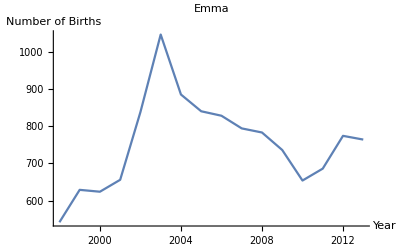

```mathematica
PlotName["Emma"]
```

### Export

Mathematica’s Export function is just as powerful as its Import function.

```mathematica
?Export
```

RowBox[{"Export", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"file\",\"TI\"]\).\!\(\*StyleBox[\"ext\",\"TI\"]\)\"",ShowStringCharacters->True], ",", StyleBox["expr", "TI"]}], "]"}] exports data to a file, converting it to the format corresponding to the file extension StyleBox["ext", "TI"]. 
RowBox[{"Export", "[", RowBox[{StyleBox["file", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["\"\!\(\*StyleBox[\"format\",\"TI\"]\)\"", ShowStringCharacters->True]}], "]"}] exports data in the specified format.
RowBox[{"Export", "[", RowBox[{StyleBox["file", "TI"], ",", StyleBox["exprs", "TI"], ",", StyleBox["elems", "TI"]}], "]"}] exports data by treating StyleBox["exprs", "TI"] as elements specified by StyleBox["elems", "TI"].

Let’s export all the words in our word list and their length. First, let’s compute our word and lengths:

```mathematica
wordsAndLengths={#,StringLength@#}&/@words
```

{{a,1},{aah,3},{aahed,5},{aahing,6},{aahs,4},{aardvark,8},109571,{zymolysis,9},{zymoplastic,11},{zymoscope,9},{zymurgy,7},{zyzzyva,7},{zyzzyvas,8}}
 |  |  |  |

First, lets export the data as a csv:

```mathematica
Export["wordsAndLengths.csv",wordsAndLengths]
```

wordsAndLengths.csv

Let’s open it up and see what it looks like.

Now, for fun, let’s draw the histogram of the string lengths. First, let’s tally the string lengths:

```mathematica
wordHist=Tally[StringLength/@words]
```

{{1,1},{3,853},{5,6919},{6,11492},{4,3130},{8,19461},{9,16693},{2,140},{7,16882},{11,8374},{10,11882},{12,5812},{13,3676},{14,2102},{16,583},{15,1159},{17,229},{20,29},{19,39},{25,1},{28,1},{21,11},{18,107},{22,4},{23,2},{0,1}}

Next, let’s ListPlot:

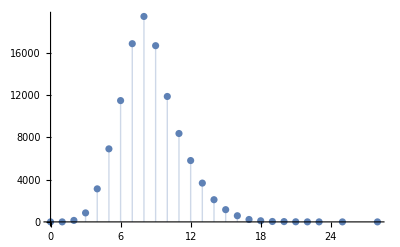

```mathematica
plot=ListPlot[wordHist,Filling->Axis]
```

We can export the histogram data as an excel file:

```mathematica
Export["wordHist.xls",wordHist]
```

wordHist.xls

Let’s take a look at it.

We can also export the plot in various formats. For instance, we can export it as a PNG:

```mathematica
Export["wordHistPlot.png",plot]
```

wordHistPlot.png

We can also export it as a PostScript:

```mathematica
Export["wordHistPlot.eps",plot]
```

wordHistPlot.eps

You can even use Export to render formulas and equations as an image:

```mathematica
Export["myEquation.eps",Sqrt[a^2+b^2]]
```

myEquation.eps